# NG^21 P_14. Репродуктивный план Холланда

## 1. Селекционная привлекательность

```mathematica
SetDirectory@NotebookDirectory[];
Get["NG21P13Problem.mx","NG21P13"]
```

```mathematica
(μ-3σ)/μ/(μ+3σ)=4/2/1
```

Set::write: Tag Times in (μ-3 σ)/(μ (μ+3 σ)) is Protected.

2

```mathematica
w==a0+a1 μ+a2 μ^2
%/.{{w->4,μ->μ-3σ},{w->2,μ->μ},{w->1,μ->μ+3σ}}
First@Solve[%,{a0,a1,a2}]
a0+a1 # +a2#^2/.%
```

w==a0+a1 μ+a2 μ^2

{4==a0+a1 (μ-3 σ)+a2 (μ-3 σ)^2,2==a0+a1 μ+a2 μ^2,1==a0+a1 (μ+3 σ)+a2 (μ+3 σ)^2}

{a0→-(-μ^2-9 μ σ-36 σ^2)/(18 σ^2),a1→-(2 μ+9 σ)/(18 σ^2),a2→1/(18 σ^2)}

-(-μ^2-9 μ σ-36 σ^2)/(18 σ^2)-((2 μ+9 σ) #1)/(18 σ^2)+#1^2/(18 σ^2)

```mathematica
ClearAll[Fitness];
Fitness[μ_,σ_]:=-(-μ^2-9 μ σ-36 σ^2)/(18 σ^2)-((2 μ+9 σ) #1)/(18 σ^2)+#1^2/(18 σ^2)&
Fitness[troubles_List]:=Fitness[Mean@troubles,StandardDeviation@troubles][troubles]
```

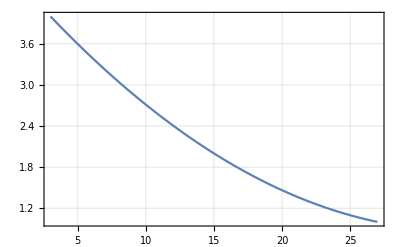

```mathematica
Plot[Fitness[##][μ],{μ,#1-3#2,#1+3#2},Frame->True,GridLines->Automatic]&[15,4]
```

```mathematica
Fig0 = ContourPlot[Troubles[{x,y,10,100}],{x,0,100},{y,0,100}, ColorFunction->"GreenPinkTones", Contours->50, ContourStyle->None]
```

## 2. Популяция

```mathematica
RandomReal[{0,1},{10,4}]//MatrixForm
{x,y,F,α}.{{100,0,0,0},{0,100,0,0},{0,0,10,0},{0,0,0,360}}
```

(0.95854 | 0.950885 | 0.920434 | 0.57832
0.509035 | 0.313461 | 0.749586 | 0.920565
0.00376043 | 0.0454869 | 0.49822 | 0.759869
0.557425 | 0.481983 | 0.198028 | 0.281542
0.264256 | 0.63355 | 0.132928 | 0.336622
0.419819 | 0.500589 | 0.0607405 | 0.555222
0.0198393 | 0.626833 | 0.737409 | 0.619852
0.997659 | 0.537272 | 0.502808 | 0.21328
0.198275 | 0.410555 | 0.181946 | 0.554877
0.211133 | 0.877822 | 0.735387 | 0.436896)

{100 x,100 y,10 F,360 α}

```mathematica
%%.{{100,0,0,0},{0,100,0,0},{0,0,10,0},{0,0,0,360}}
```

{{12.389,28.0775,6.13214,64.521},{2.99987,95.3828,5.76805,167.602},{81.7902,60.2743,6.405,83.1374},{99.1303,21.8411,7.92802,217.002},{72.3047,25.5921,8.99702,251.212},{76.223,18.4328,4.60888,194.905},{1.1094,84.598,9.62921,179.642},{31.4015,65.5272,0.97618,189.156},{83.2443,40.9668,0.383333,38.2781},{91.6574,14.6636,6.10543,18.8273}}

Из прошлой лабы

```mathematica
ClearAll[AnalogToDigital, DigitalToAnalog];
AnalogToDigital[{from_,to_},bits_Integer]:=Round[ (# - from- 2^(-1-bits))/(2^-bits(to-from))]&;
DigitalToAnalog[{from_,to_},bits_Integer]:= Round[(to-from)(from  + # 2^-bits+2^(-1-bits) ),0.1]&;
```

```mathematica
ClearAll[GrayTable, ToGray,FromGray];

ToGray[n_]:=Module[{num=IntegerDigits[n,2],numShifted},numShifted=IntegerDigits[BitShiftRight[n,1],2];
numShifted=PadLeft[numShifted,Length@num];BitXor[num,numShifted]];
ToGray[n_Integer,len_Integer]:=Module[{num=IntegerDigits[n,2,len],numShifted},numShifted=IntegerDigits[BitShiftRight[n,1],2,len];
BitXor[num,numShifted]];
GrayTable=ToGray[#]&/@ Range[0,1024];
FromGray[g_]:=  Fold[BitXor,0,FixedPointList[BitShiftRight,FromDigits[g,2]]]
```

```mathematica
ClearAll[PhenotypeToGenotype,GenotypeToPhenotype];
PhenotypeToGenotype[{x_,y_,F_,α_}]:=Flatten@MapThread[ToGray[#1,#2]&,{MapThread[AnalogToDigital[{0,#1},#2][#3]&,{{100,100,10,360},{10,10,10,9} ,{x,y,F,α}}],{10,10,10,9}}];
GenotypeToPhenotype[chromosome_]:= N@MapThread[DigitalToAnalog[{0,#1},Length[#2]][FromGray[#2]]&,{{100,100,10,360},Partition[chromosome,UpTo[10]]}];
```

```mathematica
ClearAll[Population];
SetAttributes[Population, HoldAllComplete];
(************************************)
(*** Конструктор популяции особей ***)
Population["Init",InitParams_Association]:= Association[
  "best"-> {},      (* фенотип лучшей за все поколения особи *) 
  "genotype"->{}, (* генотип популяции *)
  "phenotype"->RandomReal[{0,1},{InitParams["size"],4}].{{100,0,0,0},{0,100,0,0},{0,0,10,0},{0,0,0,360}},(* фенотип популяции *)
  "troubles"->{},  (* уровни помех особей популяции *)
  "fitness"->{},   (* приспособленности особей популяции *)
  "params"-><|(*вспомогательные параметры:*)
"size"->InitParams["size"],(*размер популяции*)
"pc"->InitParams["pc"],(*вероятность скрещивания*)
"pi"-> InitParams["pi"],(*вероятность инверсии*)
"pm"->InitParams["pm"] (*вероятность мутации*)|>]
(***************)
Options[Population]={ImageSize->{UpTo[200],UpTo[200]}};
Population[P_Symbol]["Show",opts___]:=Show[Fig0,Graphics[{Darker@ColorData["GreenPinkTones",(P["troubles"]⟦#⟧)/10],Point[P["phenotype"]⟦#,{1,2}⟧],Arrow[{P["phenotype"]⟦#,{1,2}⟧,{P["phenotype"]⟦#,1⟧ + P["phenotype"]⟦#,3⟧Cos[P["phenotype"]⟦#,4⟧ Degree],P["phenotype"]⟦#,2⟧+P["phenotype"]⟦#,3⟧Sin[P["phenotype"]⟦#,4⟧ Degree]}}]}&/@Range[P["params"]["size"]], PlotRange->{{0,100},{0,100}}]]
```

```mathematica
P0=Population["Init",<|"size"-> 10,"pc"->0.9,"pi"->0.01,"pm"->0.10|>]
```

<|best→{},genotype→{},phenotype→{{91.7685,60.8909,7.85424,344.703},{76.3933,0.0732992,1.53508,350.226},{36.158,82.2618,9.84994,275.464},{76.3147,62.2507,5.40768,182.015},{95.1033,1.30186,9.78746,248.965},{37.7166,59.6649,0.745437,163.527},{41.485,33.266,4.92399,44.9187},{38.7815,77.3393,5.89429,148.157},{81.6524,68.214,7.31821,110.916},{27.6056,23.7322,2.31376,257.501}},troubles→{},fitness→{},params→<|size→10,pc→0.9,pi→0.01,pm→0.1|>|>

```mathematica
P=P0;
P["troubles"]=Troubles/@P["phenotype"]
Min[%]
Position[%%,%,1,1]⟦1,1⟧
P["phenotype"]⟦%⟧
P[ "best"]=%
Fitness[Mean@%%%%%,StandardDeviation@%%%%%]
%[%%%%%%]
P["fitness"]=%
```

{2.02837,2.90756,7.83673,2.81287,5.37959,2.89097,4.63328,3.4061,4.88881,4.00258}

2.02837

1

{91.7685,60.8909,7.85424,344.703}

{91.7685,60.8909,7.85424,344.703}

-(-4.07869^2-9 4.07869 1.69396-36 1.69396^2)/(18 1.69396^2)-((2 4.07869+9 1.69396) #1)/(18 1.69396^2)+#1^2/(18 1.69396^2)&

{2.68657,2.37223,1.16418,2.40465,1.64878,2.37789,1.84226,2.20728,1.77359,2.02258}

{2.68657,2.37223,1.16418,2.40465,1.64878,2.37789,1.84226,2.20728,1.77359,2.02258}

```mathematica
P["best"]=P["phenotype"]⟦Position[P["troubles"],Min[P["troubles"]],1,1]⟦1,1⟧⟧
```

```mathematica
P["fitness"]=Fitness[Mean@P["troubles"],StandardDeviation@P["troubles"]][P["troubles"]]
```

{2.11888,2.62296,2.41769,1.63169,2.37576,1.29751,1.49575,1.81285,2.68159,2.04533}

```mathematica
Fitness@P["troubles"]
```

{2.11888,2.62296,2.41769,1.63169,2.37576,1.29751,1.49575,1.81285,2.68159,2.04533}

```mathematica
P
```

<|best→{91.7685,60.8909,7.85424,344.703},genotype→{},phenotype→{{91.7685,60.8909,7.85424,344.703},{76.3933,0.0732992,1.53508,350.226},{36.158,82.2618,9.84994,275.464},{76.3147,62.2507,5.40768,182.015},{95.1033,1.30186,9.78746,248.965},{37.7166,59.6649,0.745437,163.527},{41.485,33.266,4.92399,44.9187},{38.7815,77.3393,5.89429,148.157},{81.6524,68.214,7.31821,110.916},{27.6056,23.7322,2.31376,257.501}},troubles→{2.02837,2.90756,7.83673,2.81287,5.37959,2.89097,4.63328,3.4061,4.88881,4.00258},fitness→{2.68657,2.37223,1.16418,2.40465,1.64878,2.37789,1.84226,2.20728,1.77359,2.02258},params→<|size→10,pc→0.9,pi→0.01,pm→0.1|>|>

```mathematica
P["genotype"]=PhenotypeToGenotype/@ P["phenotype"];
```

```mathematica
Plus@@P["fitness"]
```

20.5

## 3. Репродуктивный план

```mathematica
ClearAll[Population];
```

```mathematica
Population[P_Symbol]["Fitness"]:=Block[{T,Ph},T=P["troubles"]=Map[Troubles,Ph=P["phenotype"]];
P["best"]=Ph⟦Position[T,Min@T,1,1]⟦1,1⟧⟧;
P["fitness"]=Fitness[Mean@T,StandardDeviation@T][T];
P["genotype"]=PhenotypeToGenotype/@ Ph;];
```

```mathematica
Population[P_Symbol]["Select"]:= First@Flatten@Position[P["genotype"],RandomChoice[P["fitness"]-> P["genotype"]]];
```

```mathematica
Population[P_Symbol]["Crossover",parent1_Integer,parent2_Integer]:= Module[{pos=RandomInteger[39]},Append[P["genotype"]⟦parent1⟧⟦;;pos⟧,P["genotype"]⟦parent2⟧⟦pos+1;;⟧]//Flatten]
```

```mathematica
Population[P]["Crossover",2,3]
```

{0,0,1,1,0,1,1,0,0,1,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0,0,1,1,1,1,1,0,1,0,1,0,0,1}

```mathematica
Population[P_Symbol]["Elimination",child_]:= P["genotype"]/.RandomChoice[P["genotype"]]->child;
```

```mathematica
P["genotype"]=Population[P]["Inversion",1]
```

{{0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,1,0,1,1,1,0,1,1,1,1,0,0,0,0,0,1,1,0,0,1,0},{0,0,1,1,0,1,1,0,0,1,0,1,0,1,0,1,1,1,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,1},{1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,0,1,0,0,1},{0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,0,1,0,0,0,0,1,1,1,0,1,1,0,0,0,0,0,1,0,1,1,0,1},{0,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,1,1,0,1,0,0,0,1,1,1,1,0,0,0,1,1,0,1,1,0,0,1,0},{0,1,1,0,1,0,1,0,1,0,0,1,1,0,1,1,1,1,1,1,1,0,1,0,0,1,0,0,0,1,0,1,1,0,1,0,1,1,0},{1,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,0,0,1,0,1,0,1,1,0,1,1,1,1,1},{1,0,0,1,0,1,1,0,1,1,1,0,0,1,0,1,1,0,0,1,0,0,0,1,0,1,1,1,0,0,1,1,0,0,0,0,0,0,1},{1,1,1,0,1,0,0,1,1,1,1,0,1,0,0,0,0,1,1,0,1,1,1,0,0,0,0,1,0,1,1,0,0,1,1,0,0,1,0},{1,1,0,1,0,1,0,0,1,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,1,1,0,1,1,1,0,1,0,0,1,0,1,1,0}}

```mathematica
Replace
```

```mathematica
Population[P_Symbol]["Inversion",individual_Integer]:= P["genotype"]/.P["genotype"]⟦individual⟧->RotateRight[P["genotype"]⟦individual⟧,RandomInteger[{1,39}]];
```

```mathematica
Population[P_Symbol]["Mutation",individual_Integer]:= Module[{bit=RandomInteger[{1,39}],m=P["genotype"]⟦individual⟧},m⟦bit⟧=m⟦bit⟧/.{0->1,1->0};P["genotype"]/.P["genotype"]⟦individual⟧->m];
```

```mathematica
First@First@Position[P["genotype"],{1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,0,1,0,0,1}]
```

## 4.

```mathematica
Population[P_Symbol]["Breeding",s_]:= Module[{par1,par2,child={},f},
Print[Population[P]["Show"]];
Population[P]["Fitness"];
Do[
par1=Population[P]["Select"];
If[RandomReal[]≤ P["params"]["pc"],par2=Population[P]["Select"];
child=Population[P]["Crossover",par1,par2];
P["genotype"]=Population[P]["Elimination",child]
];
If[child≠{},f=child,f=par1];
If[RandomReal[]<P["params"]["pi"],P["genotype"]=Population[P]["Inversion",First@First@Position[P["genotype"],f]]];
If[RandomReal[]<P["params"]["pm"],P["genotype"]=Population[P]["Mutation",First@First@Position[P["genotype"],f]]];
P["phenotype"]= GenotypeToPhenotype[#]&/@P["genotype"];
P["troubles"] = Troubles/@P["phenotype"];
P["fitness"] = Fitness[P["troubles"]];
P["best"] = P["phenotype"]⟦Position[P["troubles"], Min@P["troubles"], 1,1]⟦1,1⟧⟧;
child={}
,s];Print[Population[P]["Show"]]];
```

```mathematica
P=Population["Init",<|"size"-> 10,"pc"->0.9,"pi"->0.01,"pm"->0.10|>]
```

<|best→{},genotype→{},phenotype→{{0.0368327,42.0672,3.5098,206.009},{14.6027,60.1718,5.18963,82.9477},{76.9435,27.9212,0.17912,131.294},{44.3822,2.17588,1.30014,270.607},{44.2567,24.8421,0.757144,193.788},{26.1572,18.1461,8.87482,189.794},{4.74387,81.5621,3.80814,96.8869},{4.66683,96.3285,6.52137,183.566},{13.9489,8.29675,8.42884,13.3377},{94.6776,95.0049,3.88917,112.061}},troubles→{},fitness→{},params→<|size→10,pc→0.9,pi→0.01,pm→0.1|>|>

```mathematica
Population[P]["Fitness"]
```

```mathematica
P
```

<|best→{65.607,92.8394,1.06027,208.243},genotype→{{1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,1,1,0,0,1,0,1,0,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,1,1,0,0,1,0,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,0,1,0,1,0,1},{1,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,1,1,1,1,1,0,1,0,0,0,1,0,1,1},{1,0,0,0,1,1,1,1,0,1,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,1,1,0,1,1,0,0,1,0,1,1,0,1,0},{1,1,0,1,0,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,0,1,1,0,0,0,0,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1,0,0},{1,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,1,0,1,0,1,1,0,1,1,0,0,0,1,1,1,1,0,1},{1,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,1,1,1,0,1,1,0},{1,0,0,0,1,1,1,1,1,1,1,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,1,0,1,1,0,1,0,0,1,1,1,1,0,1,0,0}},phenotype→{{55.7309,0.622305,0.980231,139.668},{94.9612,27.8439,5.3969,251.85},{97.2524,97.4285,0.41545,170.04},{95.8879,87.8183,4.55245,76.0671},{60.9135,77.9319,3.90321,180.122},{65.607,92.8394,1.06027,208.243},{96.9984,50.7771,6.0632,28.9305},{79.721,56.8558,1.02562,63.9095},{95.7969,56.0054,0.00334846,185.474},{46.8523,22.1587,1.43207,117.322}},troubles→{2.73413,5.13207,2.57007,4.12999,3.26455,2.1315,3.42054,3.85846,2.33935,2.72949},fitness→{2.28285,1.21036,2.38319,1.56879,1.98205,2.6684,1.90046,1.6881,2.53016,2.28564},params→<|size→10,pc→0.9,pi→0.01,pm→0.1|>|>

```mathematica
Population[P]["Breeding",10]
```